## Simple Factory Robot 3

#### ACTIONS SUCCESS

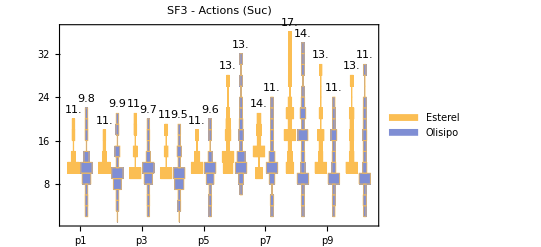

```mathematica
path="/home/tomas/ros_ws/src/ROSPlan/src/rosplan/factory_robot-results/factory_robot/problem_m3/treated_results/suc-";
list={};
For[i=1,
i≤10,
i++,
listPair={};
AppendTo[listPair,Import[path<>"esterel"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,3}]] ;
AppendTo[listPair,Import[path<>"adaptable"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,3}]];
AppendTo[list,listPair]
];
DistributionChart[list,ChartLegends->{"Esterel","Olisipo"},ChartElementFunction->"HistogramDensity",ChartLabels->{{"p1","p2","p3","p4","p5","p6","p7","p8","p9","p10"},None},LabelingFunction->(Placed[N[Mean[#],2],Above]&),BarSpacing->{0.15,0.5},PlotLabel->Style["SF3 - Actions (Suc)", 16, Bold, Black]]
```

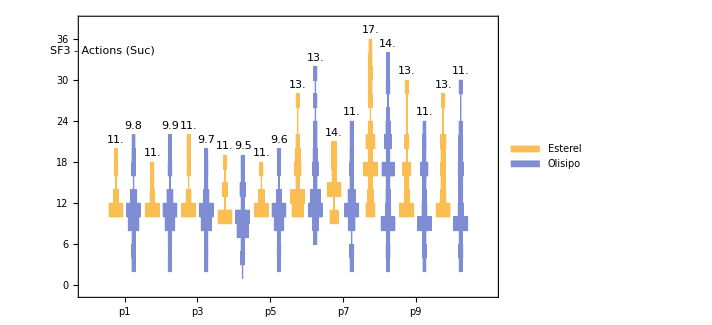

#### REPLANS SUCCESS

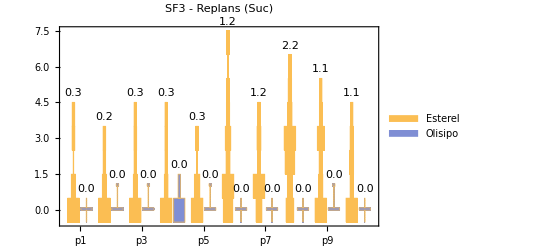

```mathematica
path="/home/tomas/ros_ws/src/ROSPlan/src/rosplan/factory_robot-results/factory_robot/problem_m3/treated_results/suc-";
list={};
For[i=1,
i≤10,
i++,
listPair={};
AppendTo[listPair,Import[path<>"esterel"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,2}]] ;
AppendTo[listPair,Import[path<>"adaptable"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,2}]];
AppendTo[list,listPair]
];
DistributionChart[list,ChartLegends->{"Esterel","Olisipo"},ChartElementFunction->"HistogramDensity",ChartLabels->{{"p1","p2","p3","p4","p5","p6","p7","p8","p9","p10"},None},LabelingFunction->(Placed[NumberForm[N[Mean[#]],{2,1}],Above]&),BarSpacing->{0.15,0.5},PlotLabel->Style["SF3 - Replans (Suc)", 16, Bold, Black]]
```

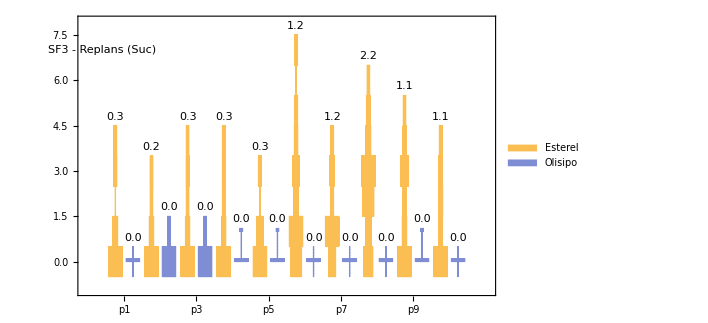

#### ACTIONS FAILURES

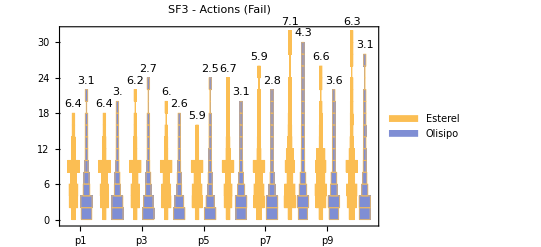

```mathematica
path="/home/tomas/ros_ws/src/ROSPlan/src/rosplan/factory_robot-results/factory_robot/problem_m3/treated_results/fail-";
list={};
For[i=1,
i≤10,
i++,
listPair={};
AppendTo[listPair,Import[path<>"esterel"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,3}]] ;
AppendTo[listPair,Import[path<>"adaptable"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,3}]];
AppendTo[list,listPair]
];
DistributionChart[list,ChartLegends->{"Esterel","Olisipo"},ChartElementFunction->"HistogramDensity",ChartLabels->{{"p1","p2","p3","p4","p5","p6","p7","p8","p9","p10"},None},LabelingFunction->(Placed[N[Mean[#],2],Above]&),BarSpacing->{0.15,0.5},PlotLabel->Style["SF3 - Actions (Fail)", 16, Bold, Black]]
```

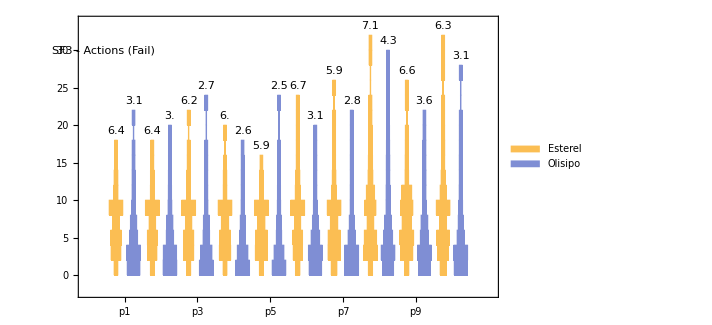

## Advanced Factory Robot 3

#### ACTIONS SUCCESS

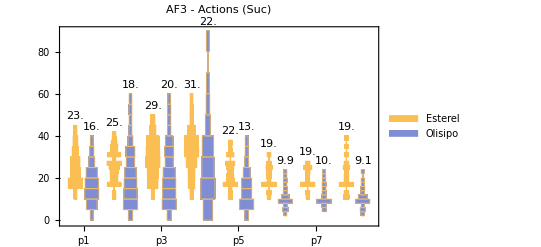

```mathematica
path="/home/tomas/ros_ws/src/ROSPlan/src/rosplan/factory_robot-results/adv_factory_robot/problem_m3/treated_results/suc-";
list={};
For[i=1,
i≤8,
i++,
listPair={};
AppendTo[listPair,Import[path<>"esterel"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,3}]] ;
AppendTo[listPair,Import[path<>"adaptable"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,3}]];
AppendTo[list,listPair]
];
DistributionChart[list,ChartLegends->{"Esterel","Olisipo"},ChartElementFunction->"HistogramDensity",ChartLabels->{{"p1","p2","p3","p4","p5","p6","p7","p8","p9","p10"},None},LabelingFunction->(Placed[N[Mean[#],2],Above]&),BarSpacing->{0.15,0.5},PlotLabel->Style["AF3 - Actions (Suc)", 16, Bold, Black]]
```

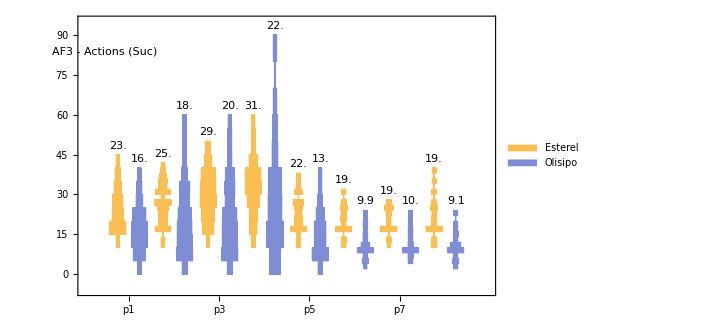

#### REPLANS SUCCESS

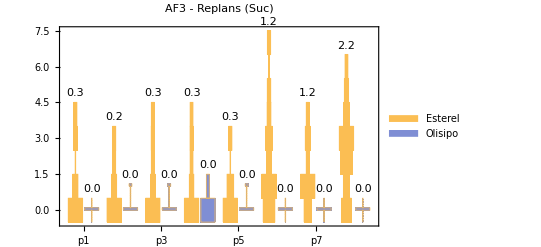

```mathematica
path="/home/tomas/ros_ws/src/ROSPlan/src/rosplan/factory_robot-results/factory_robot/problem_m3/treated_results/suc-";
list={};
For[i=1,
i≤8,
i++,
listPair={};
AppendTo[listPair,Import[path<>"esterel"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,2}]] ;
AppendTo[listPair,Import[path<>"adaptable"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,2}]];
AppendTo[list,listPair]
];
DistributionChart[list,ChartLegends->{"Esterel","Olisipo"},ChartElementFunction->"HistogramDensity",ChartLabels->{{"p1","p2","p3","p4","p5","p6","p7","p8","p9","p10"},None},LabelingFunction->(Placed[NumberForm[N[Mean[#]],{2,1}],Above]&),BarSpacing->{0.15,0.5},PlotLabel->Style["AF3 - Replans (Suc)", 16, Bold, Black]]
```

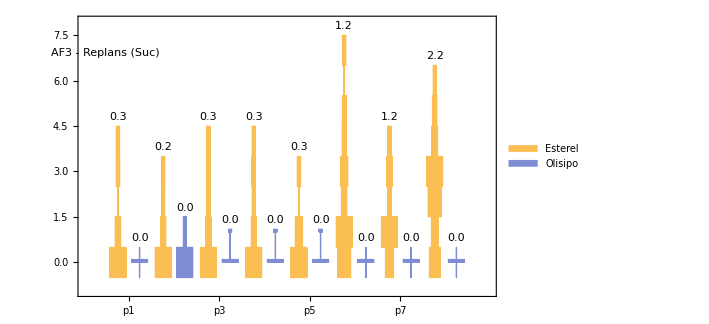

#### ACTIONS FAILURES

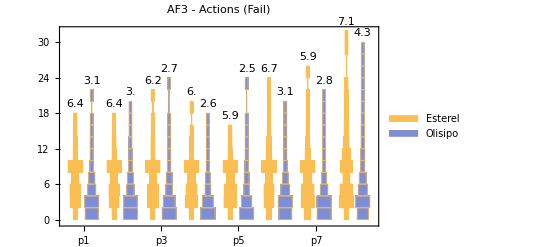

```mathematica
path="/home/tomas/ros_ws/src/ROSPlan/src/rosplan/factory_robot-results/factory_robot/problem_m3/treated_results/fail-";
list={};
For[i=1,
i≤8,
i++,
listPair={};
AppendTo[listPair,Import[path<>"esterel"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,3}]] ;
AppendTo[listPair,Import[path<>"adaptable"<>"-m3_p"<>ToString[i]<>".csv",{"Data",All,3}]];
AppendTo[list,listPair]
];
DistributionChart[list,ChartLegends->{"Esterel","Olisipo"},ChartElementFunction->"HistogramDensity",ChartLabels->{{"p1","p2","p3","p4","p5","p6","p7","p8","p9","p10"},None},LabelingFunction->(Placed[N[Mean[#],2],Above]&),BarSpacing->{0.15,0.5},PlotLabel->Style["AF3 - Actions (Fail)", 16, Bold, Black]]
```